2 - 11 Second shifting theorem, unit step function
Sketch or graph the given function, which is assumed to be zero outside the given interval. Represent it, using unit step functions. Find its transform.

3.  t - 2    (t > 2)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{t-2,t>2},{0,t<2}}],t,s]
```

ⅇ^(-2 s)/s^2

The above answer matches the text.

5.  ⅇ^t    (0<t<π/2)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{ⅇ^t,0<t<π/2},{0,t<0&&t>π/2}}],t,s]
```

(ⅇ^(-1/2 π (-1+s)) (-1+ⅇ^(1/2 π (-1+s))))/(-1+s)

```mathematica
e2=Expand[e1]
```

1/(-1+s)-ⅇ^(-1/2 π (-1+s))/(-1+s)

The above answer matches the text.

7.  ⅇ^(-π t)(2<t<4)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{ⅇ^(-π t),2<t<4},{0,t<2&&t>4}}],t,s]
```

(ⅇ^(-4 π-4 s) (-1+ⅇ^(2 π+2 s)))/(π+s)

The above answer matches the text.

9.  t^2   (t>3/2)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{t^2,t>3/2},{0,t<3/2}}],t,s]
```

(ⅇ^(-3 s/2) (8+12 s+9 s^2))/(4 s^3)

The above answer matches the text.

11.  Sin[t]    (π/2<t<π)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[Piecewise[{{Sin[t],π/2<t<π},{0,t<π/2&&t>π}}],t,s]
```

(ⅇ^(-π s) (1+ⅇ^((π s)/2) s))/(1+s^2)

The above answer matches the text.

12 - 17 Inverse transforms by the 2nd shifting theorem
Find and sketch or graph f(t) if ℒ(f) equals

13.  (6(1-ⅇ^(-π s)))/(s^2+9)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[(6 (1-ⅇ^(-π s)))/(s^2+9),s,t]
```

2 (1+HeavisideTheta[-π+t]) Sin[3 t]

The above answer is not exactly like the text. That answer refers to u(t-π) instead of Heaviside, but the two plots below make me think they are equivalent.

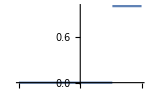

```mathematica
Plot[UnitStep[-π+t],{t,-6,6},ImageSize->150]
```

```mathematica
Plot[HeavisideTheta[-π+t],{t,-6,6},ImageSize->150]
```

-Graphics-

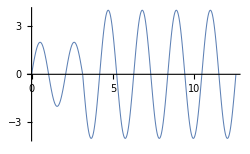

```mathematica
e2=Plot[e1,{t,0,4 π},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

The above plot looks just like the one in the s.m..

15.  ⅇ^((-3s)/s^4)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[ⅇ^(-3 s)/s^4,s,t]
```

1/6 (-3+t)^3 HeavisideTheta[-3+t]

The above answer matches the text.

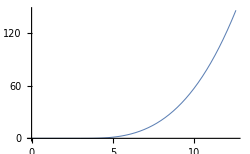

```mathematica
e2=Plot[e1,{t,0,4 π},PlotRange->Automatic,PlotStyle->Thickness[0.003],ImageSize->250]
```

17.  ((1+ⅇ^(-2π(s+1)))(s+1))/((s+1)^2+1)

```mathematica
Clear["Global`*"]
```

```mathematica
e1=InverseLaplaceTransform[((1+ⅇ^(-2 π (s+1))) (s+1))/((s+1)^2+1),s,t]
```

1/2 ⅇ^((-1-ⅈ) t) (1+ⅇ^(2 ⅈ t)) (1+HeavisideTheta[-2 π+t])

```mathematica
e2=FullSimplify[e1]
```

ⅇ^-t Cos[t] (1+HeavisideTheta[-2 π+t])

The above answer is similar to the text. The two expressions are equal when t<2 π. Though not stated in the problem, that interval is all the text answer is willing to agree to.

```mathematica
e3=Plot[e1,{t,0,3 π},PlotRange->{-.1,0.05},PlotStyle->{Yellow,Thickness[0.003]},ImageSize->350];
```

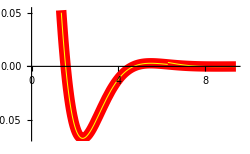

```mathematica
e4=Plot[ⅇ^-t Cos[t],{t,0,3 π},PlotRange->Automatic,PlotStyle->{Red,Thickness[0.03]},ImageSize->250];
Show[e4,e3]
```

```mathematica
e5=Plot[e1,{t,5,2 π+0.2},PlotRange->Automatic,PlotStyle->{Yellow,Thickness[0.003]},ImageSize->350];
```

```mathematica
e6=Plot[ⅇ^-t Cos[t],{t,5,2 π+0.2},PlotRange->{-.05,0.1},PlotStyle->{Red,Thickness[0.03]},ImageSize->250];
```

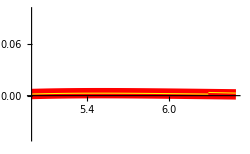

```mathematica
Show[e6,e5]
```

18 - 27 IVPs, some with discontinuous input
Using the Laplace transform and showing the details, solve

19.  y''+6y'+8y=ⅇ^(-3t)-ⅇ^(5 t),  y[0]=0, y'[0]=0

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[y''[t]+6 y'[t]+8 y[t]==ⅇ^(-3 t)-ⅇ^(-5 t),t,s]
```

8 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+6 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==1/(3+s)-1/(5+s)

```mathematica
e2=e1/.{y[0]->0,y'[0]->0,LaplaceTransform[y[t],t,s]->yoft}
```

8 yoft+6 s yoft+s^2 yoft==1/(3+s)-1/(5+s)

```mathematica
e3=Solve[e2,yoft]
```

{{yoft→2/((3+s) (5+s) (8+6 s+s^2))}}

```mathematica
e4=e3[[1,1,2]]
```

2/((3+s) (5+s) (8+6 s+s^2))

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

1/3 ⅇ^(-5 t) (-1+ⅇ^t)^3

```mathematica
y[t_]=1/3 ⅇ^(-5 t) (-1+ⅇ^t)^3
```

1/3 ⅇ^(-5 t) (-1+ⅇ^t)^3

```mathematica
y[0]
```

0

```mathematica
y'[0]
```

0

The above answer in the green cell matches the text.

21.  y'' + 9 y = 8 Sin[t] if 0 < t < π and 0 if t > π; y[0] = 0, y'[0] = 4

```mathematica
Clear["Global`*"]
```

Note that there is no shifting here; only a piecewise function definition.

```mathematica
e1=LaplaceTransform[y''[t]+9 y[t]==8 Sin[t] (1-UnitStep[t-π]),t,s]
```

9 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==8 (1/(1+s^2)+ⅇ^(-π s)/(1+s^2))

```mathematica
e2=e1/.{y[0]->0,y'[0]->4,LaplaceTransform[y[t],t,s]->bigY}
```

-4+9 bigY+bigY s^2==8 (1/(1+s^2)+ⅇ^(-π s)/(1+s^2))

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(4 ⅇ^(-π s) (2+3 ⅇ^(π s)+ⅇ^(π s) s^2))/((1+s^2) (9+s^2))}}

```mathematica
e4=e3[[1,1,2]]
```

(4 ⅇ^(-π s) (2+3 ⅇ^(π s)+ⅇ^(π s) s^2))/((1+s^2) (9+s^2))

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

4 (Cos[t]^2 Sin[t]-1/3 HeavisideTheta[-π+t] Sin[t]^3)

```mathematica
e6=e5/.HeavisideTheta[-π+t]->0
```

4 Cos[t]^2 Sin[t]

Above: This is the answer for t<π.

```mathematica
e7=e6/.(Cos[t]^2)->(1-Sin[t]^2)
```

4 Sin[t] (1-Sin[t]^2)

```mathematica
e8=Expand[e7]
```

4 Sin[t]-4 Sin[t]^3

```mathematica
e9=e8/.(-4 Sin[t]^3)->(Sin[3 t]-3 Sin[t])
```

Sin[t]+Sin[3 t]

Above: This answer matches the text for the subinterval 0<t<π.

```mathematica
e10=e5/.HeavisideTheta[-π+t]->1
```

4 (Cos[t]^2 Sin[t]-Sin[t]^3/3)

```mathematica
e11=e10/.(Sin[t]^3)->(1/4 (-Sin[3 t]+3 Sin[t]))
```

4 (Cos[t]^2 Sin[t]+1/12 (-3 Sin[t]+Sin[3 t]))

```mathematica
e12=Simplify[e11]
```

4/3 Sin[3 t]

Above: This version of the answer matches the text for the subinterval t>π.

23.  y'' + y' - 2 y = 3 Sin[t] - Cos[t] if 0 < t < 2 π and 3 Sin[2 t] - Cos[2 t] if t > 2 π; y[0] = 1, y'[0] = 0

```mathematica
Clear["Global`*"]
```

```mathematica
e1=LaplaceTransform[y''[t]+y'[t]-2 y[t]==(3 Sin[t]-Cos[t])(1-UnitStep[t-2 π])+(3 Sin[2 t]-Cos[2 t])(UnitStep[t-2 π]),t,s]
```

Note that there is no shifting here; only a piecewise function definition.

-2 LaplaceTransform[y[t],t,s]+s LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-y[0]-s y[0]-y'[0]==3/(1+s^2)-(3 ⅇ^(-2 π s))/(1+s^2)-s/(1+s^2)+(ⅇ^(-2 π s) s)/(1+s^2)+(6 ⅇ^(-2 π s))/(4+s^2)-(ⅇ^(-2 π s) s)/(4+s^2)

Above: Mathematica took a couple minutes’ think to come up with the transformation.

```mathematica
e2=e1/.{y[0]->1,y'[0]->0,LaplaceTransform[y[t],t,s]->bigY}
```

-1-2 bigY-s+bigY s+bigY s^2==3/(1+s^2)-(3 ⅇ^(-2 π s))/(1+s^2)-s/(1+s^2)+(ⅇ^(-2 π s) s)/(1+s^2)+(6 ⅇ^(-2 π s))/(4+s^2)-(ⅇ^(-2 π s) s)/(4+s^2)

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(ⅇ^(-2 π s) (-3+8 ⅇ^(2 π s)+3 s-4 ⅇ^(2 π s) s+6 ⅇ^(2 π s) s^2-ⅇ^(2 π s) s^3+ⅇ^(2 π s) s^4))/((-1+s) (1+s^2) (4+s^2))}}

```mathematica
e4=e3[[1,1,2]]
```

(ⅇ^(-2 π s) (-3+8 ⅇ^(2 π s)+3 s-4 ⅇ^(2 π s) s+6 ⅇ^(2 π s) s^2-ⅇ^(2 π s) s^3+ⅇ^(2 π s) s^4))/((-1+s) (1+s^2) (4+s^2))

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

ⅇ^t-Sin[t]-(-1+Cos[t]) HeavisideTheta[-2 π+t] Sin[t]

```mathematica
e6=e5/.HeavisideTheta[-2 π+t]->0
```

ⅇ^t-Sin[t]

Above: The answer matches the text answer for the subinterval 0<t<2 π.

```mathematica
e7=e5/.HeavisideTheta[-2 π+t]->1
```

ⅇ^t-Sin[t]-(-1+Cos[t]) Sin[t]

```mathematica
e8=Simplify[e7]
```

ⅇ^t-Cos[t] Sin[t]

```mathematica
e9=e8/.(Cos[t] Sin[t])->(1/2 Sin[2t])
```

ⅇ^t-1/2 Sin[2 t]

Above: The answer matches the text answer for the subinterval t>2 π.

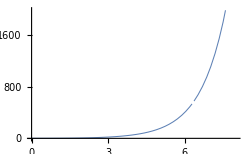

```mathematica
plot1=Plot[e5,{t,0,8},PlotRange->Automatic, PlotStyle->Thickness[0.003],ImageSize->250]
```

Notice the gap in the above plot, which is mandated by the problem description.

25.  y'' + y = t if 0 < t < 1 and 0 if t > 1;  y[0] = 0, y'[0] = 0

```mathematica
Clear["Global`*"]
```

Starting from scratch, using the info in problem 27 as a guide. There is no shifting in the problem, only the division of the domain interval. The ‘1’ in the front of (1-UnitStep[t-1]) is due to zero. See the explanation in the main text on p. 220. There would be a second term, a second UnitStep factor, except it is multiplied by zero, the ode value above 1, so it disappears.

```mathematica
e1=LaplaceTransform[y''[t]+y[t]==t(1-UnitStep[t-1]),t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==1/s^2-(ⅇ^-s (1+s))/s^2

```mathematica
e2=e1/.{y[0]->0,y'[0]->0,LaplaceTransform[y[t],t,s]->bigY}
```

bigY+bigY s^2==1/s^2-(ⅇ^-s (1+s))/s^2

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→(ⅇ^-s (-1+ⅇ^s-s))/(s^2 (1+s^2))}}

```mathematica
e4=e3[[1,1,2]]
```

(ⅇ^-s (-1+ⅇ^s-s))/(s^2 (1+s^2))

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

t-HeavisideTheta[-1+t] (t-Cos[1-t]+Sin[1-t])-Sin[t]

```mathematica
e6=e5/.HeavisideTheta[-1+t]->0
```

t-Sin[t]

Above answer is for t<1, and it matches the text answer for this subinterval.

```mathematica
e7=e5/.HeavisideTheta[-1+t]->1
```

Cos[1-t]-Sin[1-t]-Sin[t]

Above for t>1. Since Cos is even function and Sin is odd, the answer matches the text answer for this subinterval.

```mathematica
y[t_]=t-HeavisideTheta[-1+t] (t-Cos[1-t]+Sin[1-t])-Sin[t]
```

t-HeavisideTheta[-1+t] (t-Cos[1-t]+Sin[1-t])-Sin[t]

```mathematica
y[0]
```

0

```mathematica
y'[0]
```

0

```mathematica
e8=y'[t]
```

1-Cos[t]-HeavisideTheta[-1+t] (1-Cos[1-t]-Sin[1-t])-DiracDelta[-1+t] (t-Cos[1-t]+Sin[1-t])

```mathematica
plot1=Plot[e5,{t,0,3},PlotRange->Automatic, PlotStyle->Thickness[0.003],ImageSize->250];
plot2=Plot[e8,{t,0,3},PlotRange->Automatic, PlotStyle->{Red,Thickness[0.003]},ImageSize->250];
```

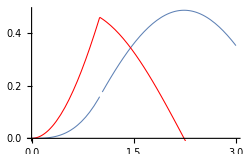

```mathematica
Show[plot1,plot2]
```

An interesting plot. The initial condition points seem to work after all.

27.  Shifted data. y''+4y=8 t^2 if 0<t<5 and 0 if t>5; y[1]=1+Cos2, y'[1]=4-2Sin[2]

```mathematica
Clear["Global`*"]
```

The initial conditions are given at t=1, but the transform calculates them for t=0; it will be necessary to shift, with t̃=t-1. Also, the unit step function comes into play, with a step of t-5, or t̃-4. Together, this changes the problem equation to: ỹ''[1+t̃]+4 ỹ[1+t̃]==8 (1+t̃)^2 (1-u[t̃-4]). (The changed version supplied by the answer in the text.)

In the version below, down to e7, t̃ is intended, but the symbol used is just t.

```mathematica
e1=LaplaceTransform[y''[t]+4 y[t]==8(1+ t)^2 (1-UnitStep[t-4]),t,s]
```

4 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==8 (2/s^3+2/s^2+1/s-ⅇ^(-4 s)/s-(2 ⅇ^(-4 s) (1+4 s))/s^2-(2 ⅇ^(-4 s) (1+4 s+8 s^2))/s^3)

Above: This is the best transcription I can manage of the equation as shown by the text.

```mathematica
e2=e1/.{y[0]->1+Cos[2], y'[0]->4-2 Sin[2],LaplaceTransform[y[t],t,s]->bigY}
```

-4+4 bigY+bigY s^2-s (1+Cos[2])+2 Sin[2]==8 (2/s^3+2/s^2+1/s-ⅇ^(-4 s)/s-(2 ⅇ^(-4 s) (1+4 s))/s^2-(2 ⅇ^(-4 s) (1+4 s+8 s^2))/s^3)

```mathematica
e3=Solve[e2,bigY]
```

{{bigY→1/(s^3 (4+s^2))ⅇ^(-4 s) (-16+16 ⅇ^(4 s)-80 s+16 ⅇ^(4 s) s-200 s^2+8 ⅇ^(4 s) s^2+4 ⅇ^(4 s) s^3+ⅇ^(4 s) s^4+ⅇ^(4 s) s^4 Cos[2]-2 ⅇ^(4 s) s^3 Sin[2])}}

```mathematica
e4=e3[[1,1,2]]
```

1/(s^3 (4+s^2))ⅇ^(-4 s) (-16+16 ⅇ^(4 s)-80 s+16 ⅇ^(4 s) s-200 s^2+8 ⅇ^(4 s) s^2+4 ⅇ^(4 s) s^3+ⅇ^(4 s) s^4+ⅇ^(4 s) s^4 Cos[2]-2 ⅇ^(4 s) s^3 Sin[2])

```mathematica
e5=InverseLaplaceTransform[e4,s,t]
```

1+4 t+2 t^2+Cos[2 (1+t)]-HeavisideTheta[-4+t] (1+4 t+2 t^2-49 Cos[8-2 t]+10 Sin[8-2 t])

```mathematica
e6=Simplify[e5]
```

1+4 t+2 t^2+Cos[2 (1+t)]-HeavisideTheta[-4+t] (1+4 t+2 t^2-49 Cos[8-2 t]+10 Sin[8-2 t])

```mathematica
e7=e6/.t->t-1
```

1+4 (-1+t)+2 (-1+t)^2+Cos[2 t]-HeavisideTheta[-5+t] (1+4 (-1+t)+2 (-1+t)^2-49 Cos[8-2 (-1+t)]+10 Sin[8-2 (-1+t)])

Above: This restores the meaning of t. It is no longer t̃, but itself, regular t.

```mathematica
e8=Expand[e7]
```

-1+2 t^2+Cos[2 t]+HeavisideTheta[-5+t]-2 t^2 HeavisideTheta[-5+t]+49 Cos[8-2 (-1+t)] HeavisideTheta[-5+t]-10 HeavisideTheta[-5+t] Sin[8-2 (-1+t)]

The above matches the text answer, if all the factors incorporating the HeavisideTheta function are evaluated according to the function definition, i.e., function equals 0 for argument less than zero.

```mathematica
e15=e8/. HeavisideTheta[-5+t]->0
```

-1+2 t^2+Cos[2 t]

The HeavisideTheta only acts as a switch to turn the adjoining factors ‘on’. For argument greater than zero, the Heaviside function returns 1. Thus the above answer is for the subinterval 0<t<5.

```mathematica
e9=e8/.HeavisideTheta[-5+t]->1
```

49 Cos[8-2 (-1+t)]+Cos[2 t]-10 Sin[8-2 (-1+t)]

```mathematica
e10=Simplify[e9]
```

49 Cos[2 (-5+t)]+Cos[2 t]-10 Sin[10-2 t]

```mathematica
e11=-Sin[x]==Sin[-x]
```

True

```mathematica
e14=Cos[x]==Cos[-x]
```

True

```mathematica
e12=e10/.{2 (-5+t)->-10+2 t}
```

49 Cos[10-2 t]+Cos[2 t]-10 Sin[10-2 t]

The above answer is equivalent to the text answer. The only differences are the signs of the arguments inside Sin and Cos, which, because of odd Sin and even Cos, agree with the text intent. For some reason I cannot use substitution commands to make Mathematica change these signs. The subinterval which this answer applies to is t>5.

39.  R = 2 Ω, L = 1 H, C = 0.5 F, v (t) = 1 kV if 0 < t < 2 and 0 if t > 2

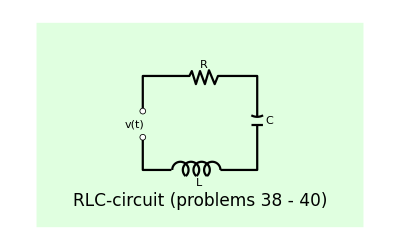

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,2.5}]},{Thickness[0.004],Line[{{1.3,1.1},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.25}}]},{Thickness[0.004],Line[{{2.63,1.25},{2.77,1.25}}]},{Thickness[0.004],Circle[{2.7,1.5},0.15,{-π/2-0.5,-π/2+0.5}]},{Thickness[0.004],Line[{{2.7,1.35},{2.7,1.85},{2.22,1.85},{2.18,1.75},{2.11,1.92},{2.06,1.75},{2,1.91},{1.95,1.75},{1.9,1.91},{1.87,1.85},{1.3,1.85},{1.3,1.42}}]},{Disk[{1.3,1.42},0.04]},{White,Disk[{1.3,1.42},0.03]},{Disk[{1.3,1.1},0.04]},{White,Disk[{1.3,1.1},0.03]},{Text[Style["v(t)",Medium],{1.2,1.26}]},{Text[Style["R",Medium],{2.05,1.99}]},{Text[Style["L",Medium],{1.99,0.54}]},{Text[Style["RLC-circuit (problems 38 - 40)",17],{2,0.32}]},{Text[Style["C",Medium],{2.85,1.3}]}},Axes->False]
```